## transcripts init

```mathematica
firstBoardChar[s_String]:=StringMatchQ[StringTake[s,1],"/"|"|"|"\\"|"Y"|"J"|"K"]
```

```mathematica
readBoardsFromTranscript[f_]:=(
Reap[
id=StringDrop[StringDrop[f,11],-4];
Pint[id];
Catch[
While[True,
r=Read[f,String];
Which[
r===EndOfFile,Break[],
StringMatchQ[r,"generating partition #"~~__],(
p=StringCases[r,"generating partition #"~~p__:>p][[1]];
Pint["partition "<>p];
r=Read[f,String];
Which[
StringMatchQ[r,"idhash "~~__~~"hardest is "~~(NumberString)~~__],(
moves=StringCases[r,"idhash "~~__~~"hardest is "~~m:NumberString~~__:>m][[1]];
board=Read[f,{String,String,String,String,String,String,String,String}];
If[And@@(firstBoardChar/@board),Sow[{{"id"->id,"partition"->p,"moves"->moves},board}],Throw[{"not a board",board},1]]
),
StringMatchQ[r,"idhash "~~__~~"hardest is null"~~__],Null,
True,Throw[{"1",r},1]
]
)
]
]
,
1
,
Print["bad",#]&
];
Close[f];
Null
][[2,1]]
)
```

```mathematica
generateDatFileNamesAndContents[transcript_]:=
(
boards=readBoardsFromTranscript[transcript];
(
rules=#[[1]];
data=#[[2]];
file="gen-"<>("id"/.rules)<>"-"<>("partition"/.rules)<>".dat";
{file,"moves: "<>("moves"/.rules)<>"\n"<>StringJoin[((ToString[#]<>"\n")&/@data)]}
)&/@boards
)
```

```mathematica
rotate[m_]:=Reverse/@Transpose[m]
```

```mathematica
empty={
{"/","-","-","-","-","-","-","\\"},
{"|"," "," "," "," "," "," ","|"},
{"|"," "," "," "," "," "," ","|"},
{"|"," "," "," "," "," "," ","|"},
{"|"," "," "," "," "," "," ","|"},
{"|"," "," "," "," "," "," ","|"},
{"|"," "," "," "," "," "," ","|"},
{"\\","-","-","-","-","-","-","/"}};
```

```mathematica
funcs={#&,rotate[#]&,rotate[rotate[#]]&,rotate[rotate[rotate[#]]]&,Transpose[#]&,Transpose[rotate[#]]&,Transpose[rotate[rotate[#]]]&,Transpose[rotate[rotate[rotate[#]]]]&};
```

```mathematica
applyTransform[level_,trans_]:=(
data=StringReplace[#,"/"|"\\"|"-"|"|"->" "]&/@Characters/@StringCases[StringReplace[level[[2]],first:Shortest[__~~"\n"]~~rest__:>rest],Shortest[a__~~"\n"]:>a];
data2=funcs[[trans]][data];
For[i=1,i≤8,i++,For[j=1,j≤8,j++,If[data2[[i,j]]==" ",data2[[i,j]]=empty[[i,j]]]]];
{level[[1]],StringReplace[level[[2]],first:Shortest[__~~"\n"]~~rest__:>first]<>StringJoin[Append[#,"\n"]&/@data2]}
)
```

## data

```mathematica
counts={#,Flatten[StringCases[ReadList[#,String],"hardest is "~~Shortest[a__]~~" moves":>ToExpression[a]]]}&/@transcriptFileNames;
```

```mathematica
Sort[Flatten[counts[[All,2]]]]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,«50964»,62,62,62,62,62,62,62,62,63,63,63,63,63,63,63,63,63,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,65,65,65,65,65,65,65,65,65,65,65,65,66,66,66,66,66,66,66,66,66,66,66,67,67,67,67,67,67,67,67,67,67,68,68,68,68,68,69,69,69,70,70,70,71,71,71,71,71,71,71,71,71,71,72,72,73,73,74,74,74,74,74,74,74,74,75,75,76,76,76,76,76,76,76,77,77,77,77,78,78,78,78,81,81,82,82,82,84,85,85,87,87,88,89,89,90,99}

```mathematica
Total[Length[#[[2]]]&/@counts]
```

51234

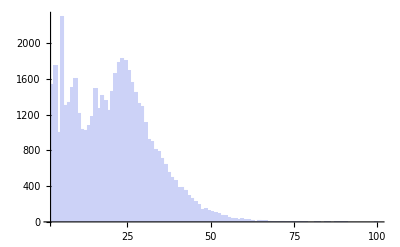

```mathematica
Histogram[Flatten[counts[[All,2]]]]
```

## read transcripts and filter levels

```mathematica
SetDirectory["C:\\Users\\brenton\\Documents\\Github\\Deadlock\\transcripts\\"];
```

```mathematica
transcriptFileNames=FileNames["transcript-*.txt",""];
```

```mathematica
a=generateDatFileNamesAndContents[#]&/@transcriptFileNames;
```

```mathematica
b=Flatten[a,1];
```

```mathematica
b=SortBy[b,StringReplace[#[[2]],"moves: "~~m:NumberString~~__:>ToExpression[m]]&];
```

```mathematica
Length[b]
```

51234

only use required moves of at least 10:

```mathematica
c=Select[b,ToExpression[StringReplace[#[[2]],"moves: "~~m:NumberString~~__:>m]]≥10&];
```

```mathematica
Length[c]
```

38892

and all boards have to have HammingDistance of at least 8 (counting all car letters as equals):

```mathematica
Dynamic[{Length[d],Length[e]}]
```

```mathematica
d=c;
e={};
While[True,
If[d=={},Break[]];
t=d[[1]];
AppendTo[e,t];
tt=StringReplace[t[[2]],RegularExpression["[ABCDEFG]"]->"A"];
d=Select[d,HammingDistance[tt,StringReplace[#[[2]],RegularExpression["[ABCDEFG]"]->"A"]]>8&];
]
```

```mathematica
SeedRandom[1]
```

```mathematica
f=applyTransform[#,RandomInteger[{1,8}]]&/@e;
```

## episode 1

```mathematica
g=f[[1;;-1;;44]];
```

```mathematica
Length[g]
```

55

```mathematica
AbsoluteTiming[Export["C:\\Users\\brenton\\Documents\\Github\\Deadlock\\BypassResources\\gen\\episode1.zip",g[[All,2]]~Join~{Length[g]},{"ZIP",({#,"Text"}&/@g[[All,1]])~Join~{{"metadata.txt","Text"}}}]]
```

{1.03178,C:\Users\brenton\Documents\Github\Deadlock\BypassResources\gen\episode1.zip}

## episode 2

```mathematica
h=DeleteCases[f,Alternatives@@g];
```

```mathematica
Length[h]
```

2341

```mathematica
i=h[[1;;-1;;4]];
```

```mathematica
Length[i]
```

586

```mathematica
AbsoluteTiming[Export["C:\\Users\\brenton\\Documents\\Github\\Deadlock\\BypassResources\\gen\\episode2.zip",i[[All,2]]~Join~{Length[i]},{"ZIP",({#,"Text"}&/@i[[All,1]])~Join~{{"metadata.txt","Text"}}}]]
```

{13.80808,C:\Users\brenton\Documents\Github\Deadlock\BypassResources\gen\episode2.zip}

## generate tutorial zip file

```mathematica
SetDirectory["C:\\Users\\brenton\\Documents\\Github\\Deadlock\\Bypass\\src\\main\\dat\\tutorial\\"];
```

```mathematica
tutorialFileNames=FileNames["tut-*.dat",""];
```

```mathematica
d={#,Import[#,"Text"]}&/@tutorialFileNames;
```

```mathematica
AbsoluteTiming[Export["C:\\Users\\brenton\\Documents\\Github\\Deadlock\\BypassResources\\gen\\tutorial.zip",d[[All,2]]~Join~{Length[d]},{"ZIP",({#,"Text"}&/@d[[All,1]])~Join~{{"metadata.txt","Text"}}}]]
```

{0.23816,C:\Users\brenton\Documents\Github\Deadlock\BypassResources\gen\tutorial.zip}